```mathematica
Get["/home/luca/repos/hyb_env_model/Mathematica/FluxInterpolation.wl"];
FluxInf[10.,0.]   (*6.15035e-5,flux to infinity,m1=1*)
FluxHor[10.,0.]   (*1.259e-8,horizon flux*)
fInf[rC,chi];fHor[rC,chi]   (*compactified r0^5 FI,r0^(15/2) FH (A13/A14)*)
rISCO[chi]   (*chi>0 prograde,chi<0 retrograde*)
FluxInf and FluxHor take the orbital radius r0 and the signed spin χ.They are valid for r0≥ISCO and|χ| ≤0.998.rISCO uses the closed-form formula,so you don't need to load KerrGeodesics.Each call takes about 27 µs.
```

0.0000615035

1.25913×10^-8

fHor[rC,chi]

rISCO[chi]

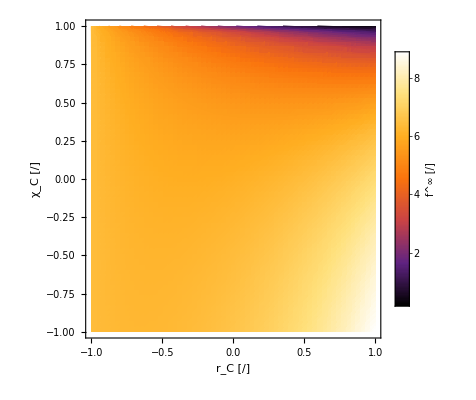

```mathematica
DensityPlot[fInf[rC,chi],{rC,-1,1},{chi,-1,1},PlotRange->All,PlotPoints->60,ColorFunction->"SunsetColors",MeshFunctions->{#3&},Mesh->20,MeshStyle->Directive[Black,Thin],Frame->True,AspectRatio->1,FrameLabel->{"\!\(\*SubscriptBox[\(r\), \(C\)]\) [/]","\!\(\*SubscriptBox[\(χ\), \(C\)]\) [/]"},PlotLegends->BarLegend[Automatic,LegendLabel->"\!\(\*SuperscriptBox[\(f\), \(∞\)]\) [/]"]]
```